```mathematica
permuteQubits[stateVec_,order_]:=Module[{n,dims},n=Log[2,Length[stateVec]];
If[Length[order]!=n,Print["Order list must have length ",n];
Return[$Failed]];
dims=ConstantArray[2,n];
Flatten[Transpose[ArrayReshape[stateVec,dims],order]]];
P0={{1,0},{0,0}};
P1={{0,0},{0,1}};
Id={{1,0},{0,1}};
Z={{1,0},{0,-1}};
Z1=KroneckerProduct[Z,Id,Id];
Z2=KroneckerProduct[Id,Z,Id];
Z3=KroneckerProduct[Id,Id,Z];
```

psitarget={0.0705533,0.127834,0.412349,-0.121442,0.539848,-0.246045,-0.374633,-0.54916}

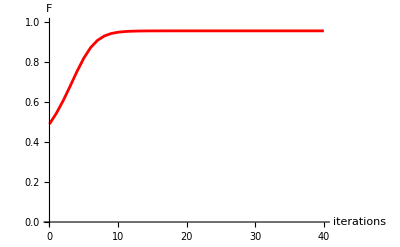

```mathematica
Np=3;
dim=2^Np;
noiter=40;
psitarget={0,1/(√3),1/(√3),0,1/(√3),0,0,0};
psitarget=Normalize[Table[RandomReal[{-1,1}],{n,1,dim}]];
psi0=psitarget;
Idbig=IdentityMatrix[dim];
p=0.2;
(*rho0=(1-p)*KroneckerProduct[Conjugate[psi0],psi0]+p*Idbig/dim;*)
rho0=(1-3*p)*KroneckerProduct[Conjugate[psi0],psi0]+p*(Z1.KroneckerProduct[Conjugate[psi0],psi0].Z1+Z2.KroneckerProduct[Conjugate[psi0],psi0].Z2+Z3.KroneckerProduct[Conjugate[psi0],psi0].Z3);
fid=Conjugate[psitarget].rho0.psitarget;
fidlist={{0,fid}};
rho=rho0;
For[j=1,j<=noiter,j=j+1,
rhop=(rho+rho.rho)/2;
prob=Tr[rhop];
rho=rhop/prob;
fid=Conjugate[psitarget].rho.psitarget;
fidlist=Append[fidlist,{j,fid}];
];
Print["psitarget=",psitarget];
p1=ListPlot[fidlist,PlotRange->{0,1},Joined->True,PlotStyle->{Red},AxesLabel->{"iterations","F"}];
Print[p1];
```